```mathematica
(*Soil Moisture PDF based on Numerical estimation of the normalization constant*)
Clear[pz,pzm,χPDF,χIavgN1,aλ,aPET, pzm, pz,pqm,PQm,σ2Qm,aλ,pχ,CC1N,ϑ, Qχ,Pχ]
(*Rainfall PDF, exponential and mixed exponential*)
pz[z_,γ_]:=γ ⅇ^(-γ z)UnitStep[z]
pzm[z_,ω_,γ1_,γ2_]:=(ω γ1 ⅇ^(-γ1 z)+(1-ω)γ2 ⅇ^(-γ2 z))UnitStep[z]
(*Soil Moisture (zero) top layer PDF *)
(*N1[DI_?NumericQ,γ_?NumericQ]:=N1[DI,γ]=1/NIntegrate[ⅇ^(-γ x0)x0^(γ/DI-1),{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)
χPDF[x0_?NumericQ,DI_?NumericQ,γ_?NumericQ]:=χPDF[x0,DI,γ]=(γ^(γ/DI)/Gamma[γ/DI,0,γ]) ⅇ^(-γ x0)x0^(γ/DI-1)(*UnitStep[1-x0]UnitStep[x0]*)
χIavg[DI_?NumericQ,γ_?NumericQ]:=χIavg[DI,γ]= (1/DI-(γ^(γ/DI-1)ⅇ^-γ)/Gamma[γ/DI,0,γ])

(*Average based on the numerical PDF*)(*DI=(γ k)/λ*)
(*χIavgN[DI_?NumericQ,γ_?NumericQ]:=χIavgN[DI,γ]=NIntegrate[x0 χPDF[x0,DI,γ],{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)

χIavgN1[DI_?NumericQ,γ_?NumericQ]:=χIavgN1[DI,γ]=UnitStep[χIavg[DI,γ]-1]+UnitStep[1-χIavg[DI,γ]]χIavg[DI,γ]

(*frequency Adjustment*)
(*Based on probability of rainfall normalized exceeding average soil spare storage capacity*)
(*PET/(α λ) α/w PDF(x=1)*)
(*PET/(α λ) α/w PDF(x=1)*)
aλ[DI_?NumericQ,γ1_?NumericQ]:=aλ[DI,γ1]=DI/γ1 χPDF[1,DI,γ1]UnitStep[1-DI/γ1 χPDF[1,DI,γ1]]+UnitStep[DI/γ1 χPDF[1,DI,γ1]-1](*ⅇ^(-(1-χIavgN[DI,γ1,0,0])γ1)*)
aPET[DI_?NumericQ,γ1_?NumericQ]:=aPET[DI,γ1]=(1-χIavg[DI,γ1])(*(1-(ⅇ^(10(DI-1))/(1+ⅇ^(10(DI-1)))))*)
(**)
ξ1=2.0; (*3.5 Lower Number Lowers Curve*)
ξ2=2.0; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.0;
ϑold[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=ϑ[LI,γs,β]=Max[-LI/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)LI/(γs^(1-.5 β^2))),0]
ξ1n=2;
ξ2n=0.5;
ξ3n=2.75;
ξ4n=-16.29;
ξ5n=-0.2;
ξ6n=0.566;
ξ7n=-1.352;
ξ8n=5;
ξ9n=57.1;
ξ10n=2.66;
(*(1+ξ5n +ξ6n β^1.5)*)
ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=Piecewise[{{Max[ⅇ^(-2(1-ξ1n β^2)LI/(γs^(1-β^2/2)))-(ξ2n+ξ3n β+ξ4n β^4.5)LI/(γs^(2(1-ξ1n β^2))),0],0<=β<=.5},{Max[ⅇ^(-LI/γs^(7/8))-(ξ7n+ξ8n β+ξ9n β^13.5)(LI/γs)^(1+ξ5n +ξ6n β^1.5),0],.5<β<1},{Max[ⅇ^(-LI/γs)-LI/γs ξ10n,0],β==1}}]

(*(DI aPET+BI)/aλ*)
(*First Moment--the Mean*)
CC1[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1[LI,γs,β,ϑ]=Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]/(Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI])(1/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
(*Take the LOg and then exp to avoid a really small number in the denominator beyond the precision of the computer*)
CC1N[LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1N[LI,γs,β,ϑ]=Exp[Evaluate[Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]]]]
pχ[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχ[x,LI,γs,β,ϑ]=CC1[LI,γs,β,ϑ]((1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))(1-x)^((γs (1-ϑ))/(1-β ϑ)))/x^(1-γs/LI)
Pχ[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=Pχ[x,LI,γs,β,ϑ]=NIntegrate[pχ[x1,LI,γs,β,ϑ],{x1,0,x}]
Qχ[P_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=Qχ[P,LI,γs,β,ϑ]=x/.FindRoot[Pχ[x,LI,γs,β,ϑ]==P,{x,0.7}]
pχPlot[x_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχPlot[x,LI,γs,β,ϑ]=(*CC1N[LI,γs,β,ϑ] *)Exp[Evaluate[Max[Log[(1-x β ϑ)^(((1-β) γs)/(β (1-β ϑ)))]+Log[(1-x)^((γs (1-ϑ))/(1-β ϑ))]-Log[(x^(1-γs/LI))]+Log[Gamma[(γs(1-ϑ))/(1-β ϑ)+1+γs/LI]]-Log[Gamma[1+(γs(1-ϑ))/(1-β ϑ)]Gamma[γs/LI]]-Log[Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ]],-700]]]
(**)
χavg[LI_,γs_,β_,ϑ_]:=γs/(γs+LI(1+γs(1-ϑ)/(1-ϑ β)))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),1+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+2+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
(*Average of the square of soil moisture*)
χ2avg[LI_,γs_,β_,ϑ_]:=((γs(LI+γs))/((γs+LI(1+γs(1-ϑ)/(1-ϑ β))) (γs+LI(2+γs(1-ϑ)/(1-ϑ β)))))(Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),2+γs/LI ,(γs(1-ϑ))/(1-β ϑ)+3+γs/LI,β ϑ]/Hypergeometric2F1[-(γs(1-β))/(β(1-β ϑ)),γs/LI ,(γs(1-ϑ))/(1-β ϑ)+1+γs/LI,β ϑ])
Budyko[DI_]:=(DI(1-ⅇ^-DI)Tanh[1/DI])^(.5)
(**)
Clear[pq,qavg,q2avg,pqm] 
pq[q_?NumericQ,LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=pq[q,LI,γs,β]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pz[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),γs]pχ[u,LI,γs ,β,ϑ[LI,γs,β]]),{u,0,1},Method->{Automatic,"SymbolicProcessing"->0} ]
(*RunoffCDF*)
PQ[Q_?NumericQ,LI_?NumericQ,γs_?NumericQ, β_?NumericQ,w_?NumericQ]:=PQ[Q,LI,γs,β,w]=NIntegrate[1/w pq[Q1/w,LI,γs,β]UnitStep[Q1],{Q1,0,Q},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->2]
(*Runoff Distribution (normalized) based on mixed exponential rainfall PDF*)
pqm[q_?NumericQ,LI_?NumericQ,γs_?NumericQ, β_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:=pqm[q,LI,γs,β,ω,γ1,γ2 ]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pzm[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),ω, γ1, γ2]pχ[u,LI,γs ,β,ϑ[LI,γs,β]])UnitStep[q],{u,0,1},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->3 ]
PQm[Q_?NumericQ,LI_?NumericQ,γs_?NumericQ, β_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:=PQm[Q,LI,γs,β,w,ω,γ1,γ2]=NIntegrate[1/w pqm[Q1/w,LI,γs,β,ω,γ1,γ2 ]UnitStep[Q1],{Q1,0,Q},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->2]
(*q= α/w-(Qbmax+PET)/(α λa) α/w*)(*Q λa= λa α-Qbmax-PET*)
qavg[LI_,γs_,β_,ϑ_]:=1/γs(1-LI χavg[LI,γs,β,ϑ])
q2avg[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=NIntegrate[q^2 pq[q,LI,γs,β],{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}]

σ2q [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:= σ2q [LI,γs,β,ϑ]=NIntegrate[pq[q,LI,γs,β](q-qavg[LI,γs,β,ϑ])^2,{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
σ2Q [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ]:= σ2Q [LI,γs,β,ϑ, w]=NIntegrate[1/w pq[Q/w,LI,γs,β](Q-w qavg[LI,γs,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
(*Variance of runoff based on mixed exponential runoff PDF*)
σ2Qm [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ, DI_?NumericQ, γ0_?NumericQ]:= σ2Qm[LI,γs,β,ϑ, w,ω,γ1,γ2, DI, γ0]=NIntegrate[1/w pqm[Q/w,LI,γs,β,ω,γ1,γ2](Q-aλ[DI,γ0]w qavg[LI,γs,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
(*4th Central Moment*)
μ4Qm [LI_?NumericQ,γs_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γ1_?NumericQ,γ2_?NumericQ]:= μ4Qm[LI,γs,β,ϑ, w,ω,γ1,γ2]=NIntegrate[1/w pqm[Q/w,LI,γs,β,ω,γ1,γ2](Q-w qavg[LI,γs,β,ϑ])^4,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
CN[S_]:=25400/((S)+254)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../Data"];
hydroParametersImport=Import["USGS_gage_hydro_variables_lwi-transition-zone.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParameters=AssociationThread[columnNames->#]&/@dataRows;

eventRunoffImport=Import["USGS_gage_event_runoff_lwi-transition-zone.csv"];
columnNames=eventRunoffImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRunoffImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRunoff=AssociationThread[columnNames->#]&/@dataRows;

eventRainfallImport=Import["USGS_gage_event_rainfall_lwi-transition-zone.csv"];
columnNames=eventRainfallImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRainfallImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../Data"];
hydroParametersImport=Import["USGS_gage_hydro_variables_jacksonville.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParameters=AssociationThread[columnNames->#]&/@dataRows;

eventRunoffImport=Import["USGS_gage_event_runoff_jacksonville.csv"];
columnNames=eventRunoffImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRunoffImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRunoff=AssociationThread[columnNames->#]&/@dataRows;

eventRainfallImport=Import["USGS_gage_event_rainfall_jacksonville.csv"];
columnNames=eventRainfallImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRainfallImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRainfall=AssociationThread[columnNames->#]&/@dataRows;
```

```mathematica
site=7
selectedRow=hydroParameters[[site]];
Print[selectedRow["usgs_site_no"]]
DI = selectedRow["DI_mean"];
Print["DI Mean ="<>ToString[DI]]
α = selectedRow["alpha_all"]/10;
Print["α ="<>ToString[α]]
λ = selectedRow["lambda_all"];
Print["λ ="<>ToString[λ]]
μ = selectedRow["mu"];
Print["μ ="<>ToString[μ]]
BI =selectedRow["BI"];
Print["BI ="<>ToString[BI]]
w=selectedRow["w"];
Print["w ="<>ToString[w]]
β=selectedRow["Beta"];
Print["β ="<>ToString[β]]
 w1 = 10 w(1-μ);
Print["w1, mm ="<>ToString[w1]]
S1val = w(1-μ)(1-χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])*10(*mm*);
Print["S, mm ="<>ToString[S1val ]]
(χavg[(DI aPET[DI,(w μ)/α]+BI)/(aλ[DI,(w μ)/α]*1.111),(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])
CNval = CN[S1val];
Print["CN ="<>ToString[CNval  ]]
muIval = (w μ(1- χIavgN1[DI,(w μ)/α]))/S1val;
Print["μ_I ="<>ToString[muIval  ]]
Qquantile50 = Q1/.FindRoot[PQ[Q1,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ)]==.5,{Q1,.5}];
Print["Qrunoff50 ="<>ToString[Qquantile50]]
χquantile50 = xq/.FindRoot[Pχ[xq,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]==.5,{xq,.5}];
Print[χquantile50 ]
Print["Baseflow50 ="<>ToString[χquantile50  *BI*α*λ]]
```

7

7376000

DI Mean =1.02009

α =2.19112

λ =0.216563

μ =0.00284818

BI =0.208076

w =109.592

β =0.1

w1, mm =1092.8

S, mm =366.757

0.713056

CN =40.9178

μ_I =0.000752675

Qrunoff50 =0.154258

0.663682

Baseflow50 =0.0655289

```mathematica
ΔP =.2; (*Probability of Each Quantile*)
Range[ΔP,1-ΔP,ΔP] (*Cumulative Probabilities, except 0 and 1*)
quantiles =Table[Qχ[P,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],{P,Range[ΔP,1-ΔP,ΔP]}]
(*Lower and Upper limts for calculating average of each quantile range*)
lowerlimits = Prepend[quantiles,0] 
upperlimits = Append[quantiles,1 ]
Table[NIntegrate[x1 pχ[x1,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/ΔP,{x1,x5[[1]],x5[[2]]}],{x5, Transpose[{lowerlimits, upperlimits}]}]
```

{0.2,0.4,0.6,0.8}

{0.588774,0.640883,0.68661,0.739931}

{0,0.588774,0.640883,0.68661,0.739931}

{0.588774,0.640883,0.68661,0.739931,1}

{0.541494,0.616095,0.663703,0.711876,0.788769}

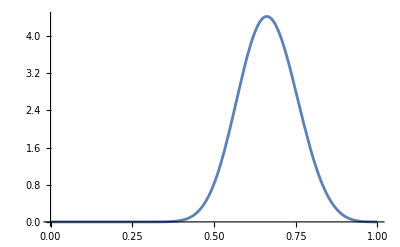

```mathematica
Plot[pχPlot[x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],{x,0,1}]
```

```mathematica
resultsLWI=Table[Module[{selectedRow,DI,α,λ , μ,BI,w,β,S1val,CNval,muIval,soilval, Qquantile ,χquantile,baseflow, Qflow},selectedRow=hydroParameters[[site]];
DI=selectedRow["DI_mean"];
α=selectedRow["alpha_all"]/10;
λ = selectedRow["lambda_all"];
μ=selectedRow["mu"];
BI=selectedRow["BI"];
w=selectedRow["w"];
β=selectedRow["Beta"];
soilval =  (χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β]]);
(*Compute S1*)
S1val=w (1-μ) (1-soilval);
(*Compute CN and muI*)
CNval=CN[S1val*10];
muIval=(w μ (1-χIavgN1[DI,(w μ)/α]))/S1val;
Qquantile = Q1/.FindRoot[PQ[Q1,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ)]==.75,{Q1,.2}];(*.05,0.2*)
Qflow =Qquantile *λ;
χquantile = xq/.FindRoot[Pχ[xq,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]==.75,{xq,.75}];(*.25, .5, .75*)
baseflow = χquantile  *BI*α*λ;
(*Store results*){β,w,w (1-μ),BI,μ,soilval,CNval,muIval,S1val,DI,α,Qflow,baseflow}],{site,Length[hydroParameters]} (*Iterate over all sites*)];
```

```mathematica
resultsJ=Table[Module[{selectedRow,DI,α,μ,BI,w,β,S1val,CNval,muIval, soilval},selectedRow=hydroParameters[[site]];
DI=selectedRow["DI_mean"];
α=selectedRow["alpha_all"]/10;
μ=selectedRow["mu"];
BI=selectedRow["BI"];
w=selectedRow["w"];
β=selectedRow["Beta"];
soilval =  (χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β]]);
(*Compute S1*)
S1val=w (1-μ) (1-soilval);
(*Compute CN and muI*)
CNval=CN[S1val 10];
muIval=(w μ (1-χIavgN1[DI,(w μ)/α]))/S1val;
(*Store results*){β,w,w (1-μ),BI,μ,soilval,CNval,muIval,S1val,DI,α}],{site,Length[hydroParameters]} (*Iterate over all sites*)];
```

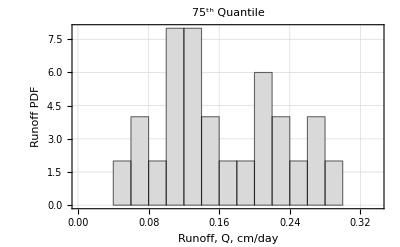

```mathematica
Histogram[resultsLWI[[All,12]],{0,.35,.02},"PDF",Frame->{{True,None},{True,None}},FrameLabel->{"Runoff, Q, cm/day","Runoff PDF"},LabelStyle->{12, Bold},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed",PlotLabel->"75^th Quantile"]
```

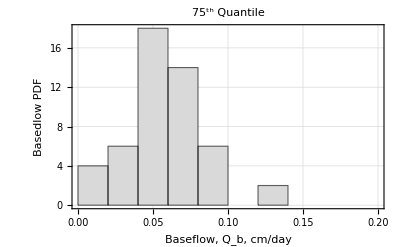

```mathematica
Histogram[resultsLWI[[All,13]],{0,.2,.02},"PDF",Frame->{{True,None},{True,None}},FrameLabel->{"Baseflow, Q_b, cm/day","Basedlow PDF"},LabelStyle->{12, Bold},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed",PlotLabel->"75^th Quantile"]
```

```mathematica
resultsLWI[[All,12]]//Mean

resultsLWI[[All,13]]//Mean
```

0.159907

0.0597994

0.0472441

7.87402

```mathematica
Textsize=14
```

14

26.778

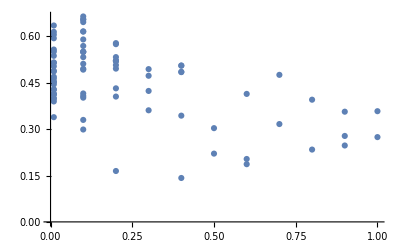

```mathematica
ListPlot[Transpose[{Flatten[{ resultsJ[[All,1]],resultsLWI[[All,1]]}],Flatten[{ resultsJ[[All,6]],resultsLWI[[All,6]]}]}],PlotRange->All]
```

```mathematica
Flatten[{ resultsJ[[All,1]],resultsLWI[[All,1]]}]//Mean
Flatten[{ resultsJ[[All,1]],resultsLWI[[All,1]]}]//Median
Print["Storage, cm"]
Flatten[{ resultsJ[[All,2]],resultsLWI[[All,2]]}]//Mean
Flatten[{ resultsJ[[All,2]],resultsLWI[[All,2]]}]//Median
Print["BI"]
Flatten[{ resultsJ[[All,4]],resultsLWI[[All,4]]}]//Mean
Flatten[{ resultsJ[[All,4]],resultsLWI[[All,4]]}]//Median
Print["mu"]
Flatten[{ resultsJ[[All,5]],resultsLWI[[All,5]]}]//Mean
Flatten[{ resultsJ[[All,5]],resultsLWI[[All,5]]}]//Median
Print["DI"]
Flatten[{ resultsJ[[All,10]],resultsLWI[[All,10]]}]//Mean
Print["alpha"]
Flatten[{ resultsJ[[All,11]],resultsLWI[[All,11]]}]//Mean
```

0.229136

0.1

Storage, cm

84.5868

48.1352

BI

0.411303

0.241078

mu

0.0397004

0.0102656

DI

1.23108

alpha

1.9898

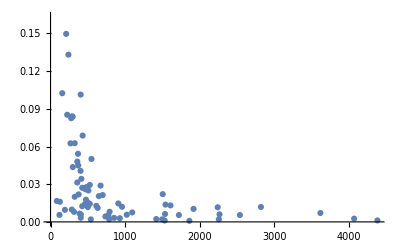

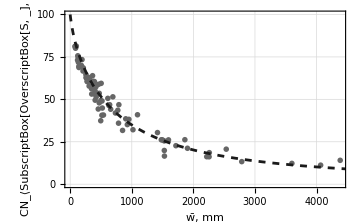

26.7467

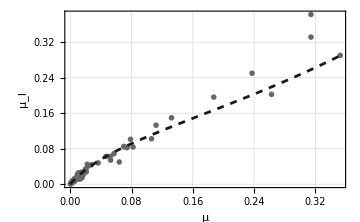

```mathematica
Show[ListPlot[Transpose[{10*Flatten[{ resultsJ[[All,2]],resultsLWI[[All,2]]}],Flatten[{ resultsJ[[All,8]],resultsLWI[[All,8]]}]}]],Plot[CN[.9 w(1-.5)],{w,0,5000},PlotRange->All]]

test1 =With[{DI=1.23,BI=.24,μ=.0102,α=1.98,β=.1}, Plot[CN[ w (1-μ)(1-χavg[(DI aPET[DI,(w/10 μ)/α]+BI)/aλ[DI,(w/10 μ)/α],(w/10 (1-μ))/α,β,ϑ[(DI aPET[DI,(w/10 μ)/α]+BI)/aλ[DI,(w/10 μ)/α],(w/10 (1-μ))/α,β]])],{w,0,4500},PlotStyle->{Dashed,GrayLevel[.1]},PlotRange->All]];
panel1nl=Show[ListPlot[Transpose[{10*Flatten[{ resultsJ[[All,3]],resultsLWI[[All,3]]}],Flatten[{ resultsJ[[All,7]],resultsLWI[[All,7]]}]}],(*PlotMarkers->Graphics[{Style[Text["x"],FontSize->14,FontWeight->Bold]}]*)PlotMarkers->Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.015]]}],PlotStyle->{GrayLevel[.4]},Frame->{{True,False},{True,False}},ImageSize->Medium,PlotTheme->"Detailed",Frame->{{True,False},{True,False}},FrameLabel->{{"CN_⟨SubscriptBox[OverscriptBox[S, _], 1]⟩",None},{"w̄, mm", None}},LabelStyle->Directive[Textsize  ,Bold],PlotRangeClipping->False,PlotRange->{0,100}],test1]


data = Transpose[{Flatten[{ resultsJ[[All,5]],resultsLWI[[All,5]]}],Flatten[{ resultsJ[[All,2]],resultsLWI[[All,2]]}]}];
MedianfilteredYValues=Last/@Select[data,First[#]>0.025&]//Median

test2 =With[{DI=1.23,BI=.24,α=1.98,β=.1,w=MedianfilteredYValues}, Plot[ (w μ(1- χIavgN1[DI,(w μ)/α]))/(w(1-μ)(1-χavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β]])),{μ,0,.35},PlotStyle->{Dashed,GrayLevel[.1]},PlotRange->All]];

panel2nl=Show[ListPlot[Transpose[{Flatten[{ resultsJ[[All,5]],resultsLWI[[All,5]]}],Flatten[{ resultsJ[[All,8]],resultsLWI[[All,8]]}]}],(*PlotMarkers->Graphics[{Style[Text["x"],FontSize->14,FontWeight->Bold]}]*)PlotMarkers->Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.015]]}],PlotStyle->{GrayLevel[.4]},Frame->{{True,False},{True,False}},ImageSize->Medium,PlotTheme->"Detailed",Frame->{{True,False},{True,False}},FrameLabel->{{"μ_I",None},{"μ", None}},LabelStyle->Directive[Textsize  ,Bold],PlotRangeClipping->False,PlotRange->All],test2]
(*ListPlot[Transpose[{10 Flatten[{ resultsJ[[All,3]],resultsLWI[[All,3]]}],Flatten[{ resultsJ[[All,6]],resultsLWI[[All,6]]}]}]]*)
```

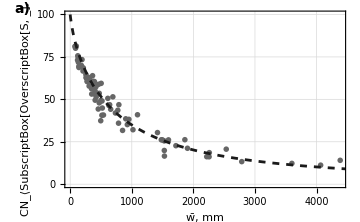

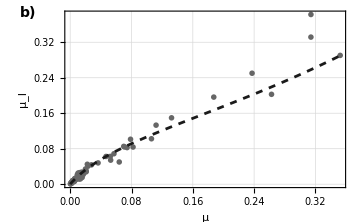

```mathematica
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.15,1.01}]]}]]
panel1=labeledPlot[panel1nl,"a)"]
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.13,.99}]]}]]
panel2=labeledPlot[panel2nl,"b)"]
```

<|0.1→62.1812,0.2→64.5629,0.01→27.83,0.4→51.4166,0.3→42.9549,0.9→33.9319,0.8→11.2226,0.6→12.5916,0.5→7.56274,0.7→31.5057,1→14.3618|>

{{0.1,62.1812},{0.2,64.5629},{0.01,27.83},{0.4,51.4166},{0.3,42.9549},{0.9,33.9319},{0.8,11.2226},{0.6,12.5916},{0.5,7.56274},{0.7,31.5057},{1,14.3618}}

FittedModel[512.371-369.302 x]

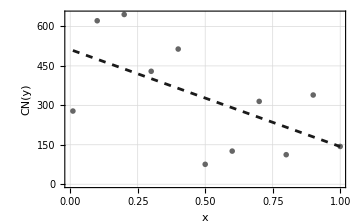

```mathematica
data=Transpose[{Flatten[{ resultsJ[[All,1]],resultsLWI[[All,1]]}],Flatten[{ resultsJ[[All,9]],resultsLWI[[All,9]]}]}];
medianData=AssociationThread[Keys[#], Mean/@Values[#]]&@GroupBy[data,First->Last]
listForm=List@@@Normal[medianData]
(*Apply CN function to y-values*)
transformedData={#[[1]],#[[2]]10}&/@listForm;

(*Fit a linear model*)
lm=LinearModelFit[transformedData,x,x]

(*Plot the data and the fitted line*)
Show[ListPlot[transformedData,AxesLabel->{"x","CN(y)"},PlotStyle->{GrayLevel[.4]},Frame->{{True,False},{True,False}},PlotMarkers->Graphics[{Style[Text["x"],FontSize->14,FontWeight->Bold]}],ImageSize->Medium,PlotTheme->"Detailed"],Plot[lm[x],{x,Min[transformedData[[All,1]]],Max[transformedData[[All,1]]]},PlotStyle->{Dashed,GrayLevel[.1]}]]
```

<|0.1→0.527286,0.2→0.477564,0.01→0.481089,0.4→0.411046,0.3→0.437775,0.9→0.293828,0.8→0.31456,0.6→0.267996,0.5→0.262012,0.7→0.395974,1→0.316124|>

{{0.1,0.527286},{0.2,0.477564},{0.01,0.481089},{0.4,0.411046},{0.3,0.437775},{0.9,0.293828},{0.8,0.31456},{0.6,0.267996},{0.5,0.262012},{0.7,0.395974},{1,0.316124}}

FittedModel[0.493713-0.22606 x]

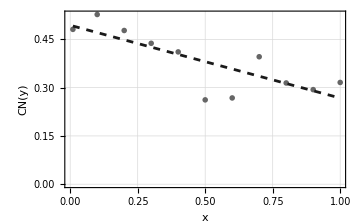

```mathematica
data=Transpose[{Flatten[{ resultsJ[[All,1]],resultsLWI[[All,1]]}],Flatten[{ resultsJ[[All,6]],resultsLWI[[All,6]]}]}];
medianData=AssociationThread[Keys[#], Mean/@Values[#]]&@GroupBy[data,First->Last]
listForm=List@@@Normal[medianData]
(*Apply CN function to y-values*)
transformedData={#[[1]],#[[2]]}&/@listForm;

(*Fit a linear model*)
lm=LinearModelFit[transformedData,x,x]

(*Plot the data and the fitted line*)
Show[ListPlot[transformedData,AxesLabel->{"x","CN(y)"},PlotStyle->{GrayLevel[.4]},Frame->{{True,False},{True,False}},PlotMarkers->Graphics[{Style[Text["x"],FontSize->14,FontWeight->Bold]}],ImageSize->Medium,PlotTheme->"Detailed"],Plot[lm[x],{x,Min[transformedData[[All,1]]],Max[transformedData[[All,1]]]},PlotStyle->{Dashed,GrayLevel[.1]}]]
```

11.2193

81.4169

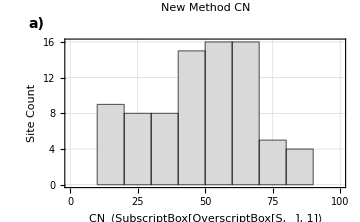

```mathematica
(*Display the results*)
data =Sort[Flatten[{ resultsJ[[All,7]],resultsLWI[[All,7]]}]];
Min[data]
Max[data]
Length[data];

part1nl= Histogram[data,{Range[0,100+2.5,10]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"CN_⟨SubscriptBox[OverscriptBox[S, _], 1]⟩","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,Textsize},ImageSize->Medium,PlotTheme->"Detailed",PlotLabel->Style["New Method CN",14,Bold]];
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.1,1.1}]]}]]
part1=labeledPlot[part1nl,"a)"]
```

0.0146766

0.0450447

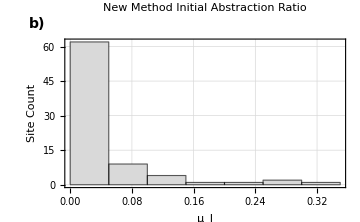

```mathematica
data =Flatten[{ resultsJ[[All,8]],resultsLWI[[All,8]]}];
data//Median
data//Mean
part2nl=Histogram[data,{Range[0,Max[data]+.005,.05*1]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"μ_I","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,Textsize},ImageSize->Medium,PlotTheme->"Detailed",PlotLabel->Style["New Method Initial Abstraction Ratio",14,Bold]];
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.1,1.1}]]}]]
part2=labeledPlot[part2nl,"b)"]
```

64.0799

83.8613

81

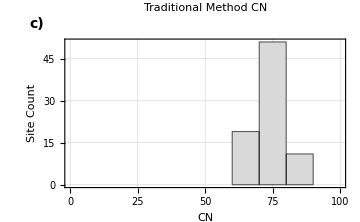

```mathematica
FLCNs={71.46356,73.58556,71.48835,68.09429,68.09429,72.21898,65.963486,76.164986,75.08468,76.3318,75.762764,74.50418,78.83771,77.32627,76.46533,69.135155,80.42793,80.953094,79.90832,81.26471,80.89023,78.78312,79.49727,78.78312,77.83508,71.055885,78.3312,83.861275,74.66653,74.66653,79.90832,71.853195,73.84178,65.292534,67.198006,67.39404,67.542816,67.7011,65.19295,68.58891,67.96961,64.33673,64.72482,66.34859,65.782646,64.079895,71.595505,70.566475,80.993385,73.67574,81.15294,81.65871,81.41071,82.30465,65.539085,67.78702};

LACNS= {76.152306,74.01401,74.02994,74.1588,79.7007,78.49967,75.11737,77.578354,74.97564,74.87911,78.35544,78.04823,80.53304,75.88827,77.018105,76.450165,75.01066,76.26698,76.088356,74.85083,77.966934,76.03195,75.035095,78.223816,79.88379};

data =Flatten[{FLCNs,LACNS}];
Min[data]
Max[data]
Length[data]

part3nl = Histogram[data,{Range[0,100+2.5,10]},(*Bins from-100 to 100 with width of 5*)"Count",Frame->{{True,None},{True,None}},FrameLabel->{"CN","Site Count"},ChartStyle->Directive[LightGray,EdgeForm[Black]],LabelStyle->{Bold,Textsize},ImageSize->Medium,PlotTheme->"Detailed",PlotLabel->Style["Traditional Method CN",14,Bold]];
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.1,1.1}]]}]]
part3=labeledPlot[part3nl,"c)"]
```

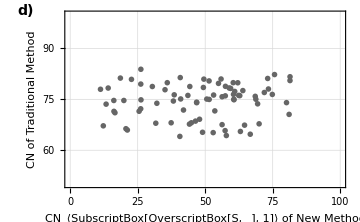

```mathematica
part4nl = ListPlot[Transpose[{Flatten[{ resultsJ[[All,7]],resultsLWI[[All,7]]}],Flatten[{FLCNs,LACNS}]}],(*PlotMarkers->Graphics[{Style[Text["x"],FontSize->14,FontWeight->Bold]}]*)PlotMarkers->Graphics[{Thickness[0.01],Circle[{0,0},Scaled[0.01]]}],PlotStyle->{GrayLevel[.4]},Frame->{{True,False},{True,False}},ImageSize->Medium,PlotTheme->"Detailed",Frame->{{True,False},{True,False}},FrameLabel->{{"CN of Traditional Method",None},{"CN_⟨SubscriptBox[OverscriptBox[S, _], 1]⟩ of New Method", None}},LabelStyle->Directive[Textsize  ,Bold],PlotRangeClipping->False,PlotRange->{{0,100},{50,100}}];
labeledPlot[fig_,label_]:=Show[fig,Graphics[{Text[Style[label,Bold,14],Scaled[{-0.14,1.0}]]}]]
part4=labeledPlot[part4nl,"d)"]
```

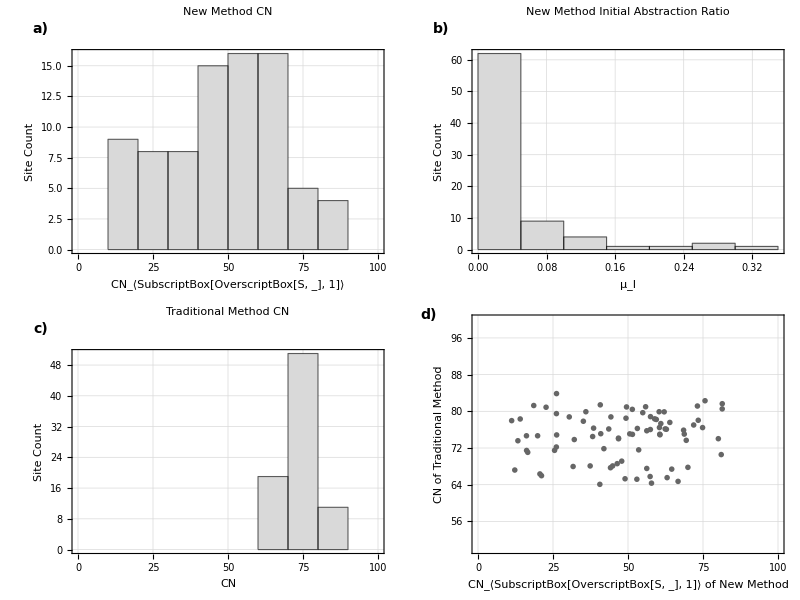

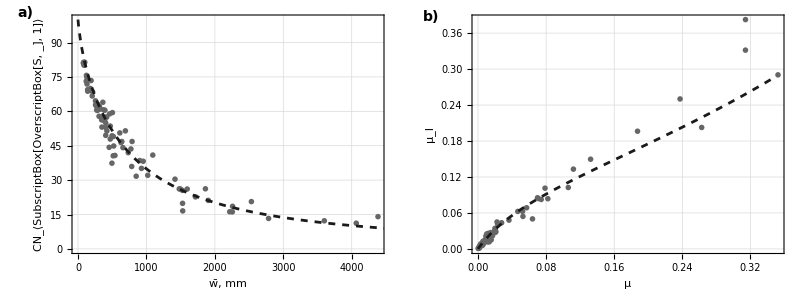

```mathematica
grid1=Grid[{{part1,part2},{part3,part4}},Spacings->{2,1}]
grid2=Grid[{{panel1,panel2}},Spacings->{2,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"Data"];
Export["Figure10.eps",grid1]
Export["Figure11.eps",grid2]
```

Fig.CN.1.eps

Fig.CN.2.eps